```mathematica
AppendTo[$Path,"C:\\Users\\hp\\Desktop\\Wolfram Summer School\\project\\Tile\\GeneralTile"];
Get["happycluster.wl"]
Get["toptile.wl"]
```

# Analysis

## 1/3+1/3+1/3

```mathematica
codes=Map[Prepend[#,{0,0}]&,SortBy[Last/@#&]@oneThirdTheoremListCluster,{2}];
```

```mathematica
graphs=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@#]&/@codes;
```

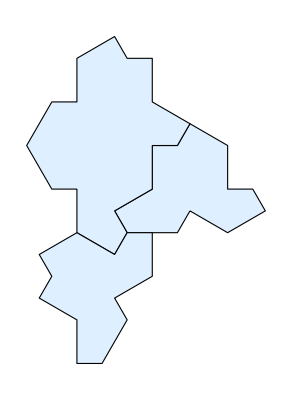
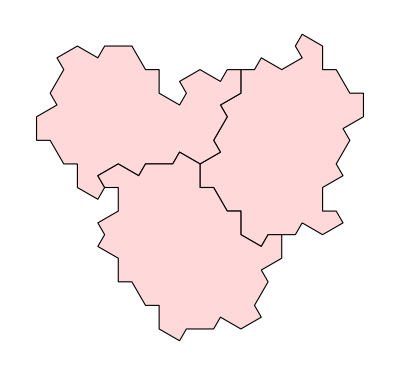
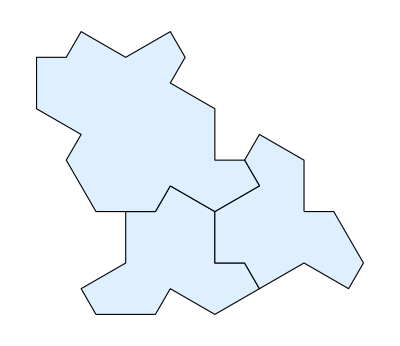
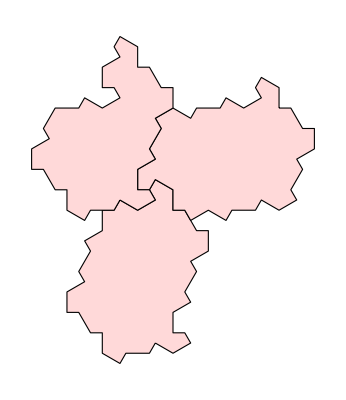
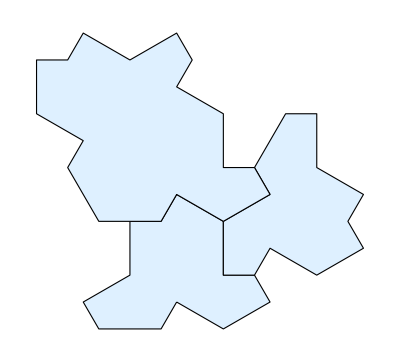
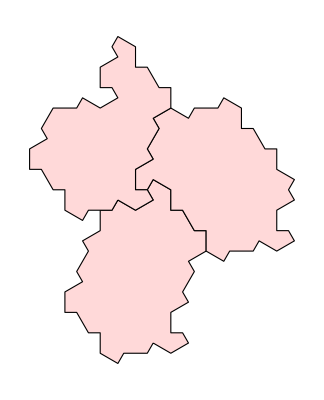
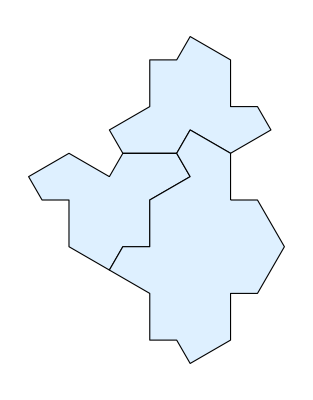
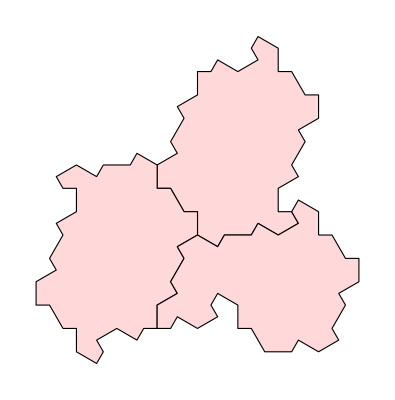
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-

```mathematica
Row[{Graphics[
{
EdgeForm[Black],
{LightBlue,metaTile[#[[1]],#[[2]],2,#[[4]]]}&/@#
}]&@buildClusterCodes[h2Tile,h1Tile][#],
Style["↔",40,Red],
Graphics[
{
EdgeForm[Black],
{LightRed,cluster[#[[1]],#[[2]],4,#[[4]]]}&/@#
}]&@buildClusterCodes[h7Tile,h8Tile][#]
}]&/@graphs//Partition[#,UpTo[4]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

## 1/3+2/3

### Group Them

```mathematica
codes=Map[Prepend[#,{0,0}]&,oneThirdAndTwoThirdTheoremListCluster,{2}];
```

```mathematica
groups=KeySortBy[Sort@*Last][GroupBy[codes,
Sort[Sort/@Values[{#[[1]],#[[2,4]]}&/@#&/@Select[clusterPointsInformation[#],Length[#]>=2&]]]&
]];
groups//Length
```

17

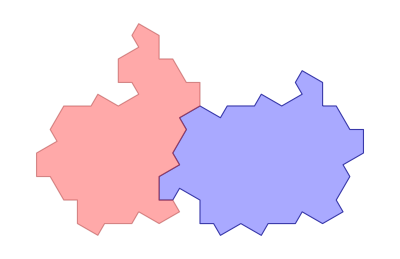
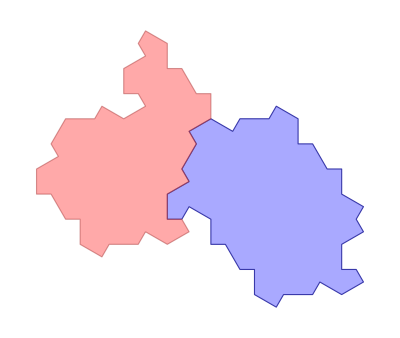
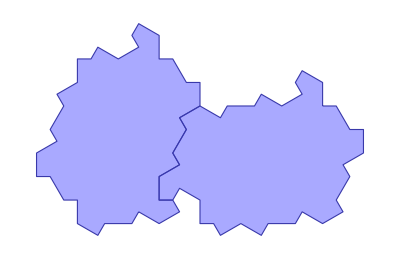
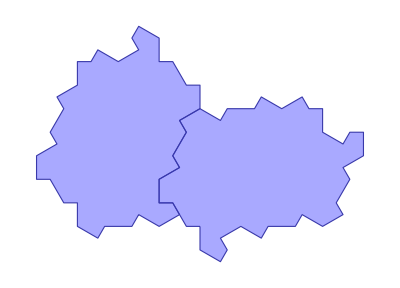
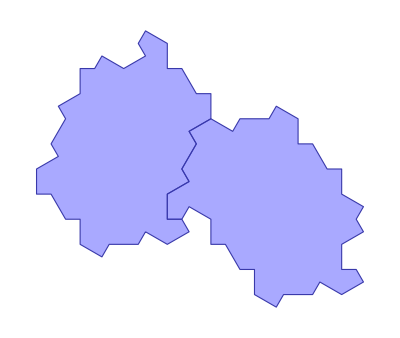
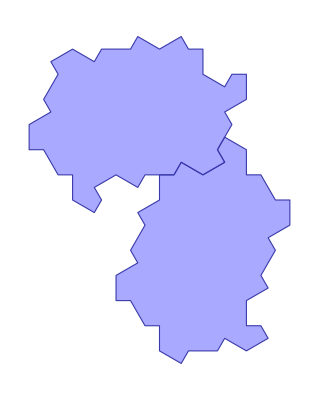
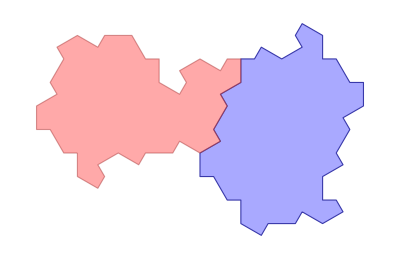
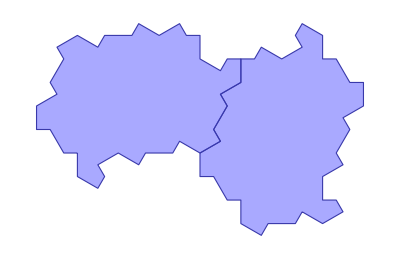

```mathematica
Map[visualize,Values@groups[[All,1]],{1}]//Row
```

```mathematica
graphs=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@#]&/@(First/@Values[groups]);
```

```mathematica
unconnected=Select[graphs,!ConnectedGraphQ[Graph[#["edge"]]]&];
connected=Select[graphs,ConnectedGraphQ[Graph[#["edge"]]]&];
```

### Connect graphs equivalent to hat tiling

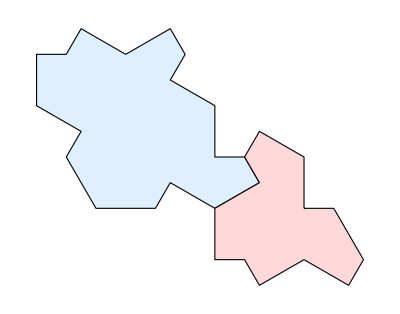
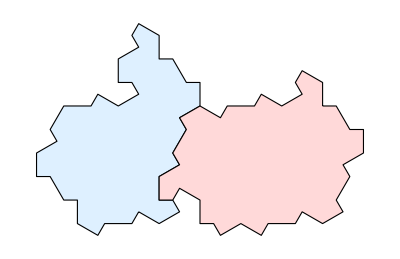
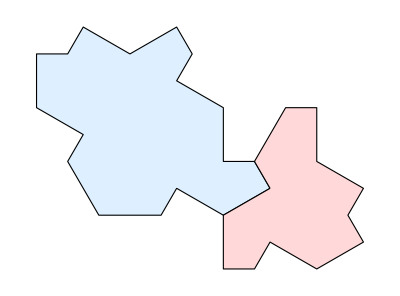
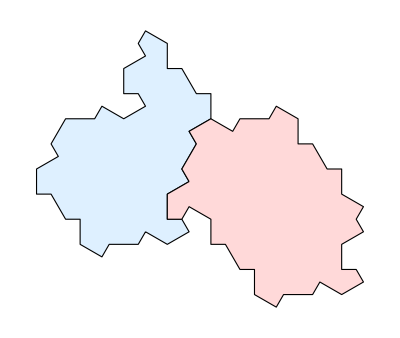
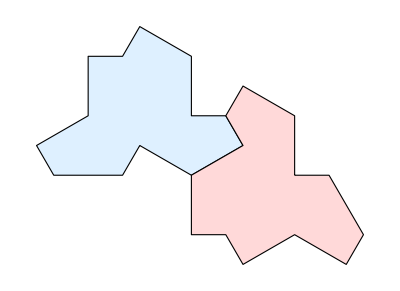
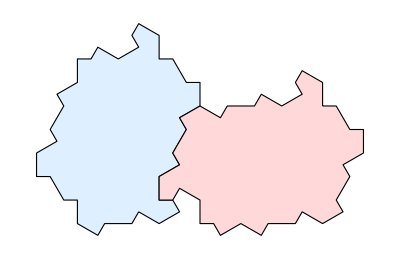
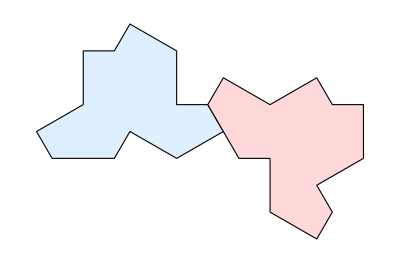
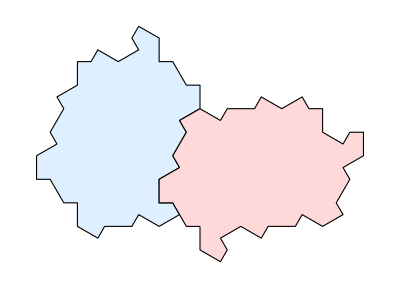
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- |  |  |

```mathematica
Row[{Graphics[
{
EdgeForm[Black],LightBlue,metaTile[#1[[1]],#1[[2]],2,#1[[4]]],
LightRed,metaTile[#2[[1]],#2[[2]],2,#2[[4]]]
}]&@@buildClusterCodes[h2Tile,h1Tile][#],
Style["↔",40,Red],
Graphics[
{
EdgeForm[Black],LightBlue,cluster[#1[[1]],#1[[2]],4,#1[[4]]],
LightRed,cluster[#2[[1]],#2[[2]],4,#2[[4]]]
}]&@@buildClusterCodes[h7Tile,h8Tile][#]
}]&/@connected//Partition[#,UpTo[4]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

### Unconnected graphs forced into a cluster equivalent to hat tiling

Since they are unconnected, we can grow them until the graph is connected.

```mathematica
unconnectedIndex=Position[graphs,Alternatives@@unconnected];
```

```mathematica
children=growH8Tiling[clusterTilingState[#],branchNumLimit->Infinity]&/@Values[groups[[All,1]]][[Flatten[unconnectedIndex]]];//Timing
```

{3.28125,Null}

```mathematica
Length/@children
```

{1,1,1,1}

```mathematica
childrenGraphs=tilingTopologicalGraph[<|False->h7Tile,True->h8Tile|>][{(clusterVertices@@#)[[4]],#[[2]],1,#[[4]]}&/@First[#]["code"]]&/@children;
```

Interesting thing is that they are all forced into some configuration, shown as only one branch as above.

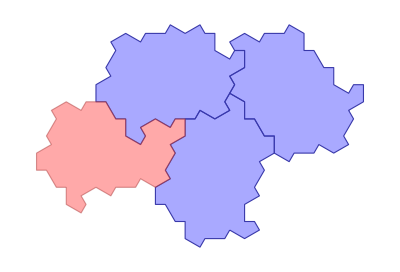
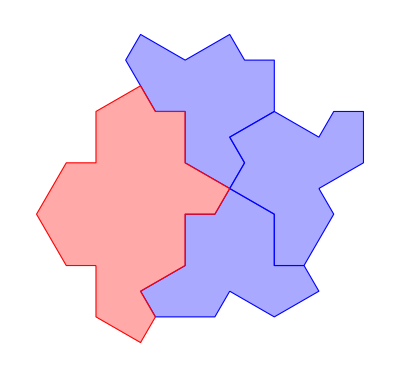
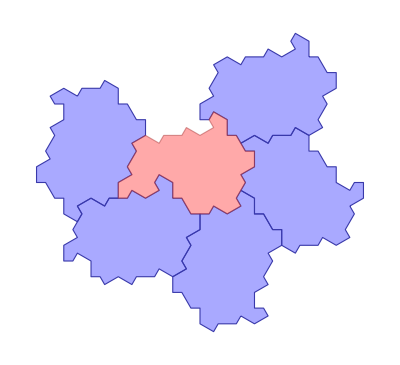
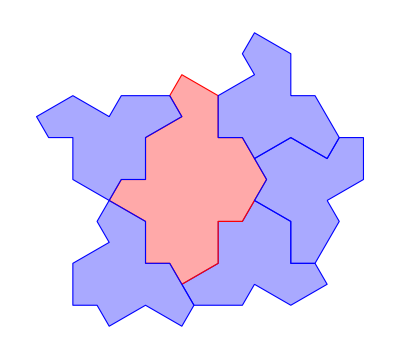
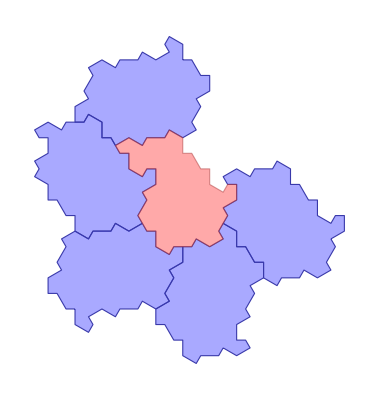
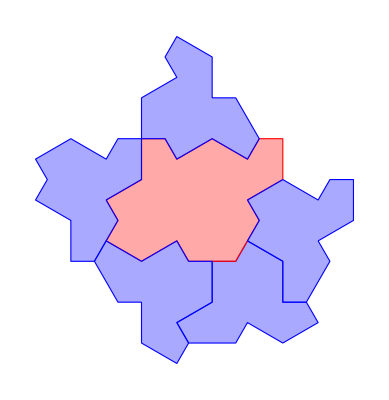
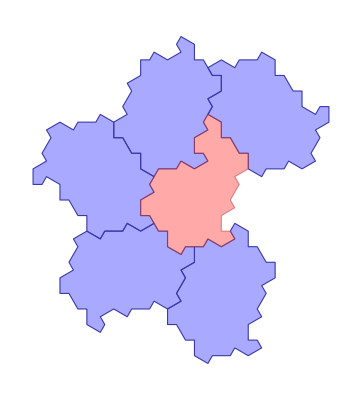
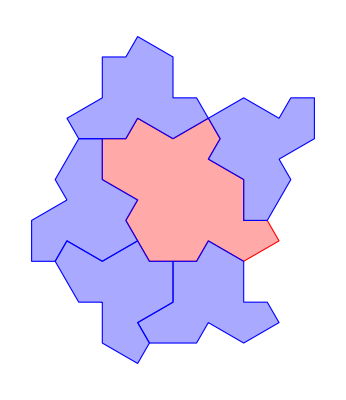
-Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics- | -Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics-
-Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics- | -Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics-

```mathematica
MapThread[
Row[{
visualize[#1],
Style["→^(grow force)",20,Red],
visualize[First[#2]["code"]],
Style["(↔^combinatorics)_equivalent",20,Red],
Graphics[
{
{EdgeForm[If[TrueQ[#[[4]]],Blue,Red]],If[TrueQ[#[[4]]],Lighter@Blue,Lighter@Red],Opacity[.5],metaTile[#[[1]],#[[2]],2,#[[4]]]}&/@#
}]&@buildClusterCodes[h2Tile,h1Tile][#3]
}]
&,
{Values[groups[[All,1]]][[Flatten[unconnectedIndex]]],children,childrenGraphs}]//Partition[#,UpTo[2]]&//Grid[#,Frame->All,FrameStyle->LightGray]&
```

We can see they are all combinatorics equivalent.

# Summary

## 1/3+1/3+1/3

-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-

## 1/3+2/3

This part has two parts, the first one part shows 13 1/3+2/3 vertex configurations can be equivalent to hat tiling directly; the second part shows the rest 4 v.f. are forced into some clusters, which produce connected topological graphs and are equivalent to hat tiling.

### Part 1

-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics- | -Graphics-↔-Graphics-
-Graphics-↔-Graphics- |  |  |

### Part 2

-Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics- | -Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics-
-Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics- | -Graphics-→^(grow force)-Graphics-(↔^combinatorics)_equivalent-Graphics-